## Tahm — PS 2 — 2025-01-21

```mathematica
Chapter 5 
List[Reverse[Range[10]^2]]
```

{{100,81,64,49,36,25,16,9,4,1}}

```mathematica
Total[Range[10]^2]
```

385

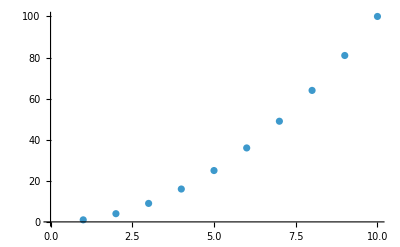

```mathematica
ListPlot[Range[10]^2]
```

```mathematica
Sort[Join[Range[3],Range[3]]]
```

{1,1,2,2,3,3}

```mathematica
9+Range[11]
```

{10,11,12,13,14,15,16,17,18,19,20}

```mathematica
List[Sort[Join[(Range[5]^2),(Range[5]^3)]]]
```

{{1,1,4,8,9,16,25,27,64,125}}

```mathematica
Length[IntegerDigits[2^128]]
```

39

```mathematica
First[IntegerDigits[2^128]]
```

3

```mathematica
Take[IntegerDigits[2^100],10]
```

{1,2,6,7,6,5,0,6,0,0}

```mathematica
Max[IntegerDigits[2^20]]
```

8

```mathematica
Count[IntegerDigits[2^1000], 0]
```

28

```mathematica
Part[Sort[IntegerDigits[2^20]],2]
```

1

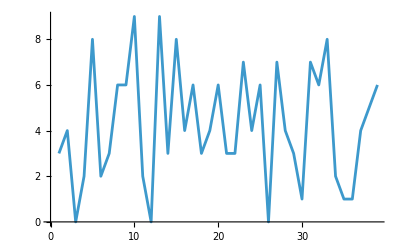

```mathematica
ListLinePlot[IntegerDigits[2^128]]
```

```mathematica
Take[Drop[Range[100],10],10]
```

{11,12,13,14,15,16,17,18,19,20}

Chapter 6

```mathematica
Table[1000,5]
```

{1000,1000,1000,1000,1000}

```mathematica
Table[n^3,{n,10,20}]
```

{1000,1331,1728,2197,2744,3375,4096,4913,5832,6859,8000}

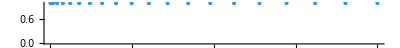

```mathematica
NumberLinePlot[Range[20]^2]
```

```mathematica
Table[n,{ n,2,20,2}]
```

{2,4,6,8,10,12,14,16,18,20}

```mathematica
Table[n,{n,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

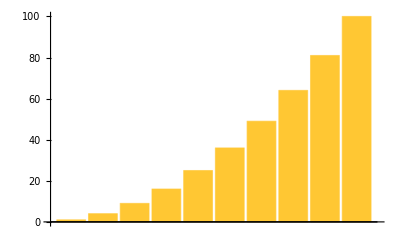

```mathematica
BarChart[Range[10]^2]
```

```mathematica
Table[IntegerDigits[n^2],{n, 1,10}]
```

{{1},{4},{9},{1,6},{2,5},{3,6},{4,9},{6,4},{8,1},{1,0,0}}

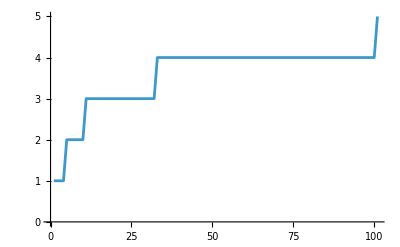

```mathematica
ListLinePlot[Table[Length[IntegerDigits[n^2]],{n, 0,100}]]
```

```mathematica
Table[First[IntegerDigits[n^2]],{n, 20}]
```

{1,4,9,1,2,3,4,6,8,1,1,1,1,1,2,2,2,3,3,4}

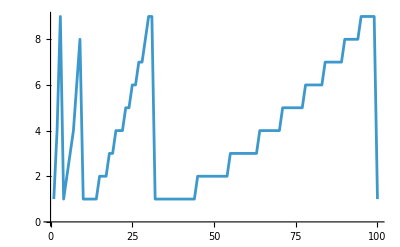

```mathematica
ListLinePlot[Table[First[IntegerDigits[n^2]],{n, 100}]]
```

Chapter 7

Syntax::bktmcp: Expression "{n,0,20,2" has no closing "}".

```mathematica
{Red, Yellow, Green}
```

{RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0]}

```mathematica
Column[{Red, Yellow, Green}]
```

RGBColor[1, 0, 0]
RGBColor[1, 1, 0]
RGBColor[0, 1, 0]

```mathematica
ColorNegate[Orange]
```

RGBColor[0., 0.5, 1.]

```mathematica
Table[Hue[x],{x,0,1.5,0.1}]
```

{Hue[0.],Hue[0.1],Hue[0.2],Hue[0.30000000000000004],Hue[0.4],Hue[0.5],Hue[0.6000000000000001],Hue[0.7000000000000001],Hue[0.8],Hue[0.9],Hue[1.],Hue[1.1],Hue[1.2000000000000002],Hue[1.3],Hue[1.4000000000000001],Hue[1.5]}

```mathematica
Table[Hue[RGBColor[1,x,1]],{x,0,1,.05}]
```

{Hue[0.8333333333333334, 1., 1.],Hue[0.8333333333333334, 0.95, 1.],Hue[0.8333333333333334, 0.9, 1.],Hue[0.8333333333333334, 0.85, 1.],Hue[0.8333333333333334, 0.8, 1.],Hue[0.8333333333333334, 0.75, 1.],Hue[0.8333333333333334, 0.7, 1.],Hue[0.8333333333333334, 0.6499999999999999, 1.],Hue[0.8333333333333334, 0.6, 1.],Hue[0.8333333333333334, 0.55, 1.],Hue[0.8333333333333334, 0.5, 1.],Hue[0.8333333333333334, 0.44999999999999996, 1.],Hue[0.8333333333333334, 0.3999999999999999, 1.],Hue[0.8333333333333334, 0.35, 1.],Hue[0.8333333333333334, 0.29999999999999993, 1.],Hue[0.8333333333333334, 0.25, 1.],Hue[0.8333333333333334, 0.19999999999999996, 1.],Hue[0.8333333333333334, 0.1499999999999999, 1.],Hue[0.8333333333333334, 0.09999999999999998, 1.],Hue[0.8333333333333334, 0.04999999999999993, 1.],Hue[0., 0., 1.]}

```mathematica
Blend[{RGBColor[1,0,1],RGBColor[ 1,1,0]}]
```

RGBColor[1, Rational[1, 2], Rational[1, 2]]

```mathematica
Table[Blend[{Yellow,Hue[x]}], {x,0,1,0.05}]
```

{RGBColor[1., 0.5, 0.],RGBColor[1., 0.65, 0.],RGBColor[1., 0.8, 0.],RGBColor[1., 0.9500000000000001, 0.],RGBColor[0.8999999999999999, 1., 0.],RGBColor[0.75, 1., 0.],RGBColor[0.5999999999999999, 1., 0.],RGBColor[0.5, 1., 0.050000000000000044],RGBColor[0.5, 1., 0.20000000000000018],RGBColor[0.5, 1., 0.3500000000000001],RGBColor[0.5, 1., 0.5],RGBColor[0.5, 0.8499999999999999, 0.5],RGBColor[0.5, 0.6999999999999997, 0.5],RGBColor[0.5, 0.5499999999999998, 0.5],RGBColor[0.6000000000000001, 0.5, 0.5],RGBColor[0.75, 0.5, 0.5],RGBColor[0.9000000000000004, 0.5, 0.5],RGBColor[1., 0.5, 0.44999999999999973],RGBColor[1., 0.5, 0.2999999999999998],RGBColor[1., 0.5, 0.1499999999999999],RGBColor[1., 0.5, 0.]}

```mathematica
Table[Style[x,Hue[x]],{x,0,1,0.1}]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
Style[ Purple,100]
```

RGBColor[0.5, 0, 0.5]

```mathematica
Table[Style[Red,x],{x,10,100,10}]
```

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0]}

```mathematica
Style[999,Red,100]
```

999

```mathematica
Table[Style[x^2,x^2],{x,1,10,1}]
```

{1,4,9,16,25,36,49,64,81,100}

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
Part[{Red,Yellow, Green},RandomInteger[{1,3},100]]
```

{RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 0, 0],RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0],RGBColor[1, 1, 0]}

```mathematica
Table[Style[Part[IntegerDigits[2^1000],n],3*Part[IntegerDigits[2^1000],n]],{n,1,50,1}]
```

{1,0,7,1,5,0,8,6,0,7,1,8,6,2,6,7,3,2,0,9,4,8,4,2,5,0,4,9,0,6,0,0,0,1,8,1,0,5,6,1,4,0,4,8,1,1,7,0,5,5}

Chapter 8



```mathematica
Graphics[RegularPolygon[3]]
```

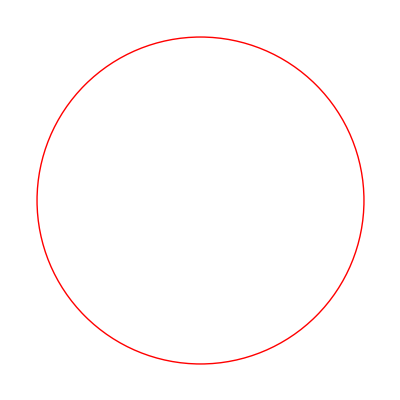

```mathematica
Graphics[Style[Circle[],Red]]
```

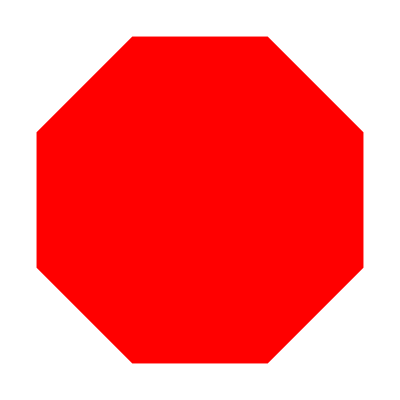

```mathematica
Graphics[Style[RegularPolygon[8], Red]]
```


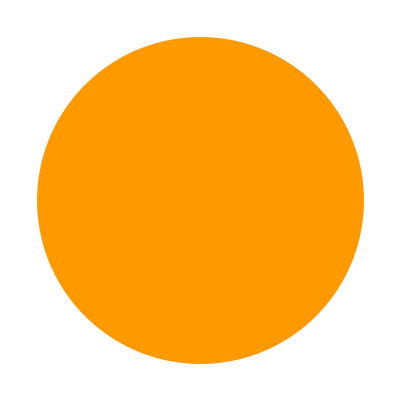
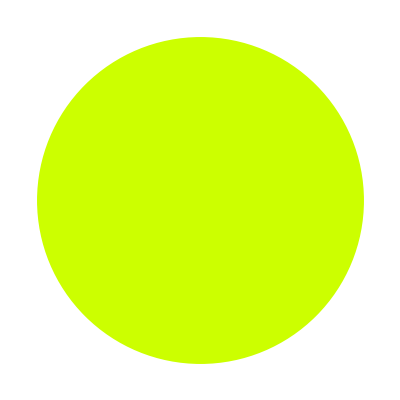
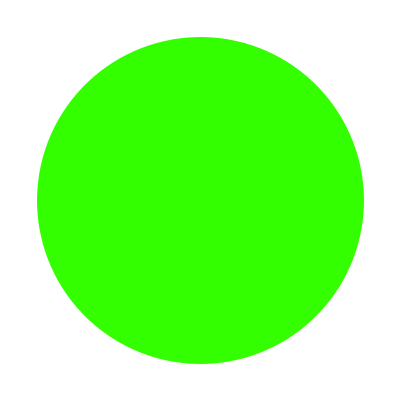
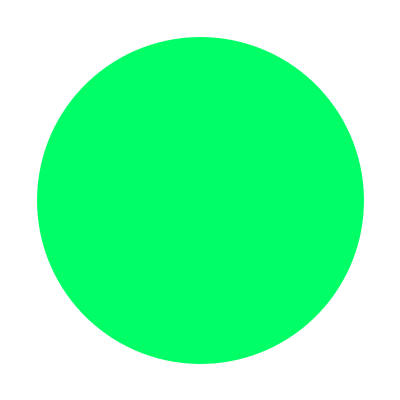
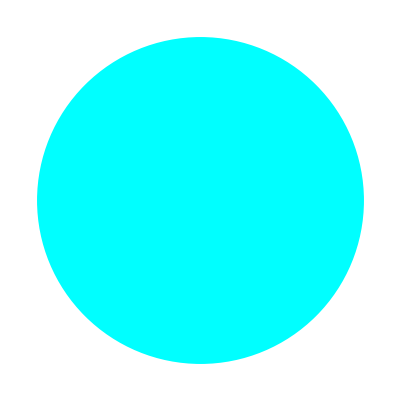
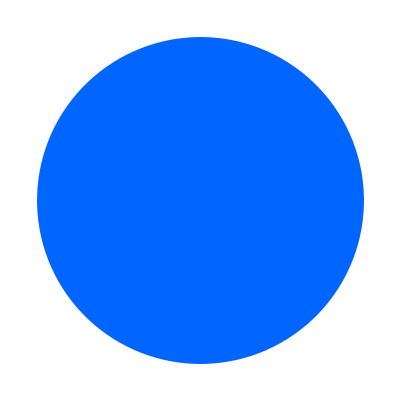
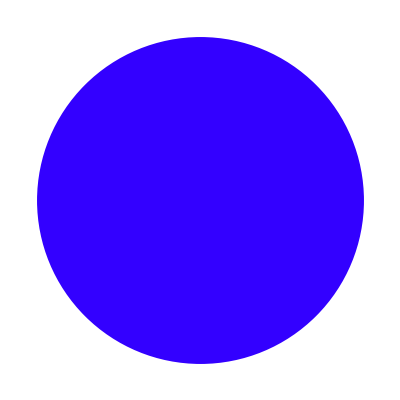
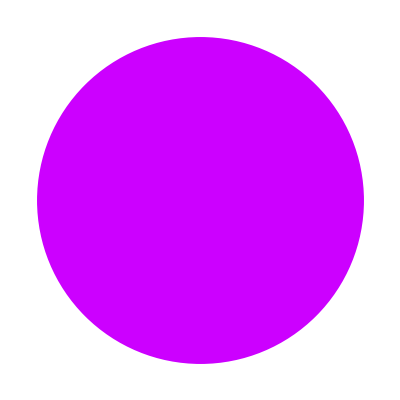
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
Table[Graphics[Style[Disk[], Hue[x]]],{x,0,1,0.1}]
```

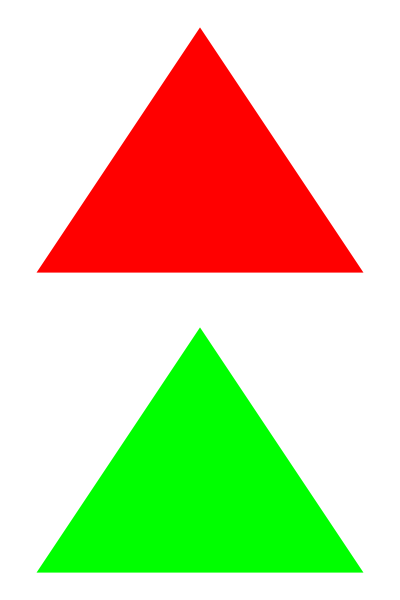

```mathematica
Column[{Graphics[Style[RegularPolygon[3], Red]], Graphics[Style[RegularPolygon[3], Green]]}]
```

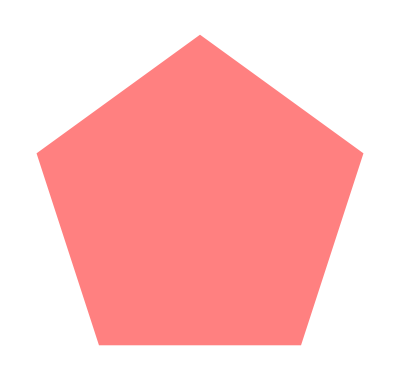
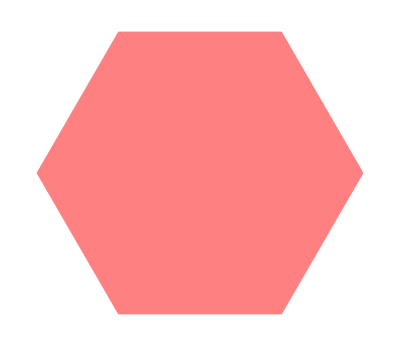
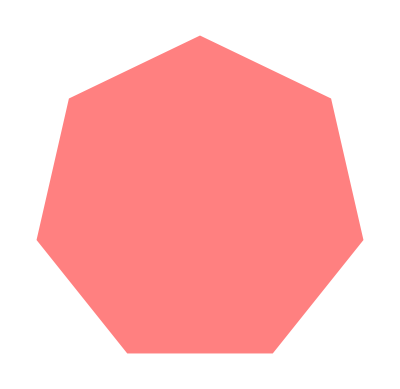
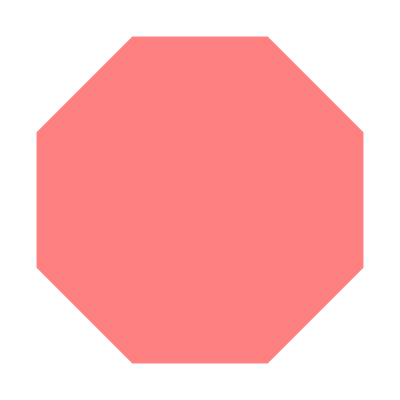
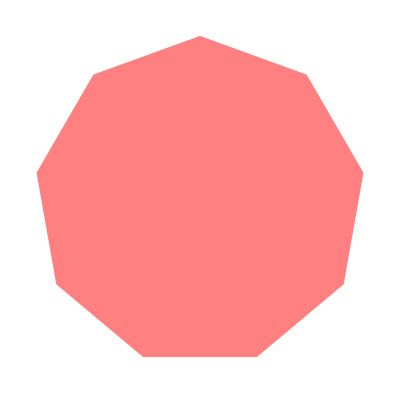
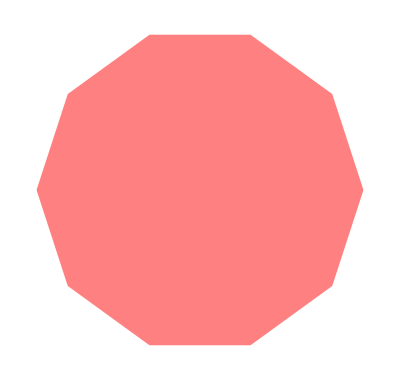

```mathematica
Table[Graphics[Style[RegularPolygon[x], Pink]], {x,5,10,1}]
```

```mathematica
Graphics3D[Style[Cylinder[], Purple]]
```

-Graphics3D-

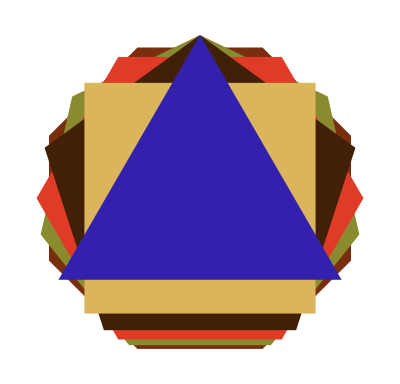

```mathematica
Graphics[Reverse[Table[Style[RegularPolygon[x], RandomColor[x]], {x,3,8,1}]]]
```